```mathematica
n=10000;
```

```mathematica
Clear[nats]
nats[0]=Floor[Sqrt[#]*10]&/@Range[10000];
step[i_]:=
(tmp=nats[i-1];
tmp[[RandomInteger[{1,n}]]]=tmp[[RandomInteger[{1,n}]]];
nats[i]=tmp;)
```

```mathematica
step/@Range[100000];
```

```mathematica
?Count
```

Count[list,pattern] gives the number of elements in list that match pattern. 
Count[expr,pattern,levelspec] gives the total number of subexpressions matching pattern that appear at the levels in expr specified by levelspec. 
Count[pattern] represents an operator form of Count that can be applied to an expression.

```mathematica
Tally[Tally[nats[0]][[All,2]]]
```

{{1,50},{2,50},{3,50},{4,50},{5,50},{6,50},{7,50},{8,50},{9,50},{10,50},{11,50},{12,50},{13,50},{14,50},{15,50},{16,50},{17,50},{18,50},{19,50},{20,25}}

```mathematica
Count[Tally[nats[0]][[All,2]],199]
```

1

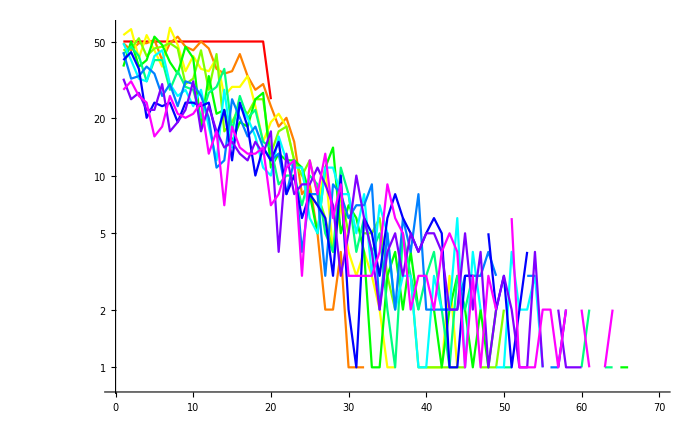

```mathematica
ListLogPlot[Table[
Table[{j,Count[Tally[nats[i]][[All,2]],j]},{j,0,70}]
,
{i,0,100000,10000}
],Joined->True,PlotRange->All,PlotStyle->(Hue/@Range[0,1,1/12])]
```

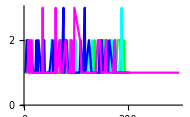

```mathematica
ListPlot[Table[({#1,#2})&@@@Sort[Tally[Tally[nats[i]][[All,2]]]],{i,10^Range[0,5]}],Joined->True,PlotRange->All,PlotStyle->(Hue/@Range[0,1,1/6])]
```

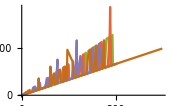

```mathematica
ListPlot[Table[({#1,#1 #2})&@@@Sort[Tally[Tally[nats[i]][[All,2]]]],{i,10^Range[0,5]}],Joined->True,PlotRange->All]
```

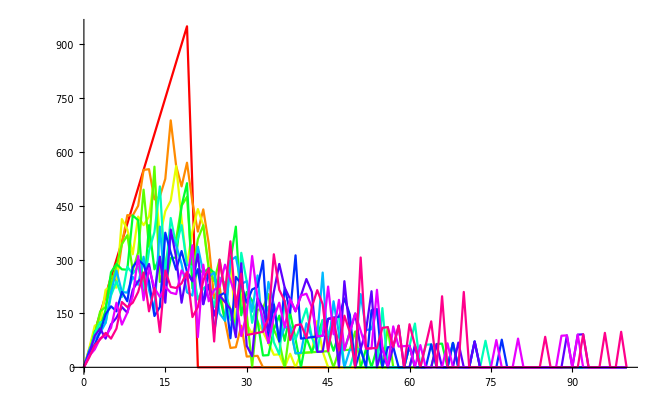

```mathematica
ListPlot[Table[
Table[{j,j*Count[Tally[nats[i]][[All,2]],j]},{j,0,100}]
,
{i,0,100000,10000}
],Joined->True,PlotRange->All,PlotStyle->(Hue/@Range[0,1,1/11])]
```